```mathematica
sVars={"i","j","k","l"};tVars={"m","n"};

Phi[x_]=1/2 (1+Erf[x/(√2)]);
(*Averages in case of an Erf teacher and student needed in order to formulate the dynamics and compute the generalization error*)
I2Erf[C2_]:=(2 ArcSin[C2⟦1,2⟧/(√(1+C2⟦1,1⟧) √(1+C2⟦2,2⟧))])/π;
I3Erf[C3_]:=(2 (C3⟦2,3⟧ (1+C3⟦1,1⟧)-C3⟦1,2⟧ C3⟦1,3⟧))/(π √((1+C3⟦1,1⟧) (1+C3⟦3,3⟧)-C3⟦1,3⟧^2) (1+C3⟦1,1⟧));
I4Erf[C4_]:=Module[{Λ0,Λ1,Λ2,Λ4},Λ4=(1+C4⟦1,1⟧) (1+C4⟦2,2⟧)-C4⟦1,2⟧^2;Λ0=Λ4 C4⟦3,4⟧-C4⟦2,3⟧ C4⟦2,4⟧ (1+C4⟦1,1⟧)-C4⟦1,3⟧ C4⟦1,4⟧ (1+C4⟦2,2⟧)+C4⟦1,2⟧ C4⟦1,3⟧ C4⟦2,4⟧+C4⟦1,2⟧ C4⟦1,4⟧ C4⟦2,3⟧;Λ1=Λ4 (1+C4⟦3,3⟧)-C4⟦2,3⟧^2 (1+C4⟦1,1⟧)-C4⟦1,3⟧^2 (1+C4⟦2,2⟧)+2 C4⟦1,2⟧ C4⟦1,3⟧ C4⟦2,3⟧;Λ2=Λ4 (1+C4⟦4,4⟧)-C4⟦2,4⟧^2 (1+C4⟦1,1⟧)-C4⟦1,4⟧^2 (1+C4⟦2,2⟧)+2 C4⟦1,2⟧ C4⟦1,4⟧ C4⟦2,4⟧;Return[(4 ArcSin[Λ0/(√Λ1 √Λ2)])/(π^2 √Λ4)];];
(*Averages in case of a ReLU teacher and student*)
I2ReLU[C2_]:=1/4 C2⟦1,2⟧+(√(C2⟦1,1⟧ C2⟦2,2⟧-C2⟦1,2⟧^2))/(2 π)+(C2⟦1,2⟧ ArcSin[C2⟦1,2⟧/(√(C2⟦1,1⟧ C2⟦2,2⟧))])/(2 π);
I3ReLU[C3_]:=(C3⟦1,2⟧ √(C3⟦1,1⟧ C3⟦3,3⟧-C3⟦1,3⟧^2))/(2 π C3⟦1,1⟧)+(C3⟦2,3⟧ ArcSin[C3⟦1,3⟧/(√(C3⟦1,1⟧ C3⟦3,3⟧))])/(2 π)+1/4 C3⟦2,3⟧;
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];

(*NOT IMPORTANT FOR NOW: Ignore the following averages, experimental*)
I4ReLU11[C2_]:=1/4 C2⟦2⟧⟦2⟧+(((C2⟦1⟧⟦2⟧)/(C2⟦1⟧⟦1⟧)-2) √(C2⟦1⟧⟦1⟧ C2⟦2⟧⟦2⟧-(C2⟦1⟧⟦2⟧)^2))/(2 π)+((C2⟦2⟧⟦2⟧-2 C2⟦1⟧⟦2⟧) ArcSin[(C2⟦1⟧⟦2⟧)/(√(C2⟦2⟧⟦2⟧ C2⟦1⟧⟦1⟧))])/(2 π)-1/2 C2⟦1⟧⟦2⟧+1/2 C2⟦1⟧⟦1⟧;
I2ErfReLU[C2_]:=C2⟦1,2⟧/(√(2 π) √(1+C2⟦2,2⟧));
I3ErfReLU[C3_]:=C3⟦2,3⟧/(√(2 π) √(1+C3⟦2,2⟧));
I3ReLUErf[C3_]:=(√(2/π) (-C3⟦1,2⟧ C3⟦1,3⟧+(1+C3⟦1,1⟧) C3⟦2,3⟧))/(√(2 π) (1+C3⟦1,1⟧)^(3/2));
HelperReLU[varList_]:=Return[0];

(*Not important: This section deals with returning the correct symbol (order parameter) for a covariance between two variables*)
getCovar[var1_,var2_]:=(If[MemberQ[sVars,First[var1]],If[MemberQ[sVars,First[var2]],If[Last[var1]≤Last[var2],Return[Subscript[Q, Last[var1],Last[var2]][α]],Return[Subscript[Q, Last[var2],Last[var1]][α]]],Return[Subscript[R, Last[var1],Last[var2]][α]]],If[MemberQ[sVars,First[var2]],Return[Subscript[R, Last[var2],Last[var1]][α]],Return[T⟦Last[var1],Last[var2]⟧]]];);

createCoVar[varList_]:=Module[{returnMat,r,c},d=Length[varList];returnMat=ConstantArray[0,{d,d}];For[r=1,r≤d,r++,For[c=r,c≤d,c++,returnMat⟦r,c⟧=If[d==2,getCovar[varList⟦r⟧,varList⟦c⟧],getCovar[varList⟦r⟧,varList⟦c⟧]];returnMat⟦c,r⟧=returnMat⟦r,c⟧;]];returnMat];

(*IMPORTANT: This function formulates the dynamical equations for the desired system*)
(*TODO: Simplify significantly*)
FormulateDynamics[actTeach_,actStud_]:=Module[{eqnsR, eqnsQ, eg},
Switch[actStud,
"ReLU",I2Stud=I2ReLU;I3Stud=I3ReLU;I4=HelperReLU;assumps=Flatten[{RAssumptionsReLU,QAssumptionsReLU}];If[actTeach=="ReLU",I2Teach=I2ReLU;I2Cross=I2ReLU;I3Teach=I3ReLU;I4Teach=I4ReLU;,I2Teach=I2Erf;I2Cross=I2ErfReLU;I3Teach=I3ErfReLU;],
"Erf",I2Stud=I2Erf;I3Stud=I3Erf;I4Stud=I4Erf;If[actTeach=="ReLU",I2Teach=I2ReLU;I2Cross=I2ErfReLU;I3Teach=I3ReLUErf;assumps=Flatten[{RAssumptionsReLU,QAssumptionsReLU}],I2Teach=I2Erf;I2Cross=I2Erf;I3Teach=I3Erf;I4Teach=I4Erf]];


(*Here the equations are formulated using the correct averages I2, I3 and I4*)
eqnsR=Flatten[Table[Subscript[R, i,n]'[α]==Simplify[η (∑_m^M I3Teach[createCoVar[{{"i",i},{"n",n},{"m",m}}]]-∑_j^K I3Stud[createCoVar[{{"i",i},{"n",n},{"j",j}}]]),assumps],{i,1,K},{n,1,M}]];eqnsQ={};For[i=1,i≤K,i++,For[k=i,k≤K,k++,eqnsQ=Append[eqnsQ,Subscript[Q, i,k]'[α]==η (∑_m^M I3Teach[createCoVar[{{"i",i},{"k",k},{"m",m}}]]-∑_j^K I3Stud[createCoVar[{{"i",i},{"k",k},{"j",j}}]]+∑_m^M I3Teach[createCoVar[{{"k",k},{"i",i},{"m",m}}]]-∑_j^K I3Stud[createCoVar[{{"k",k},{"i",i},{"j",j}}]])+η^2 (∑_m^M ∑_n^M I4Teach[createCoVar[{{"i",i},{"k",k},{"n",n},{"m",m}}]]-2 ∑_n^M ∑_j^K I4Teach[createCoVar[{{"i",i},{"k",k},{"j",j},{"n",n}}]]+∑_l^K ∑_j^K I4Teach[createCoVar[{{"i",i},{"k",k},{"j",j},{"l",l}}]])]]];
(*Onderstaand stuk is gebruikt voor de single-layer ReLU perceptron, omdat hiervoor de eta^2 term hoogstens 2d averages bevat.*)
(*η^2 I4ReLU11[{{Subscript[Q, 1,1][α],Subscript[R, 1,1][α]},{Subscript[R, 1,1][α],T⟦1⟧⟦1⟧}}]*) 
(*Side effect of this function: the generalization error for this architecture is globally defined*)
eg[α_]:=1/2 (∑_(i=1)^K ∑_(j=1)^K I2Stud[createCoVar[{{"i",i},{"j",j}}]]-2 ∑_(i=1)^K ∑_(m=1)^M I2Cross[createCoVar[{{"i",i},{"m",m}}]]+∑_(m=1)^M ∑_(n=1)^M I2Teach[createCoVar[{{"m",m},{"n",n}}]]);
Return[<|R->eqnsR,Q->eqnsQ,generr->eg[α]|>]
];

(*solveEqns[Rinit_,Qinit_,vinit_,winit_,Rs_,Qs_,vs_,ws_]:=(solutions=First[NDSolve[Join[Flatten[eqnsR],ReleaseHold[eqnsQ],Flatten[Rinit],Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];For[i=1,i≤K,i++,For[n=1,n≤M,n++,Subscript[r, i,n]=Subscript[R, i,n]/.solutions⟦(i-1) M+n⟧;]];count=1;For[i=1,i≤K,i++,For[k=i,k≤K,k++,Subscript[q, i,k]=Subscript[Q, i,k]/.solutions⟦K M+count⟧;count++;]];);*)

createReLUAssumptions[M_,K_]:=(RAssumptionsReLU:=Table[(Subscript[R, i,m][α])^2≤Subscript[Q, i,i][α] T⟦m⟧⟦m⟧&&Subscript[R, i,m][α]∈Reals,{i,1,K},{m,1,M}];QAssumptionsReLU:=Table[Subscript[Q, i,j][α]^2≤Subscript[Q, i,i][α] Subscript[Q, j,j][α]&&Subscript[Q, i,j][α]∈Reals&&If[i==j,Subscript[Q, i,j][α]≥0],{i,1,K},{j,1,K}];);
```

-Graphics-

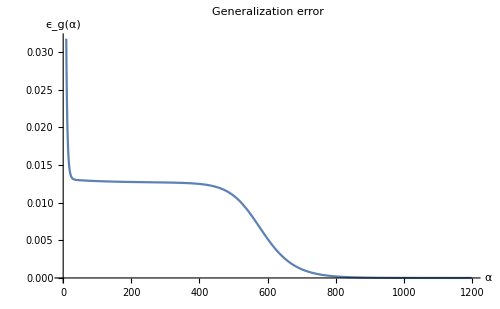

```mathematica
(*Parameters like for example weight decay γ and drift paramater δ can be assigned before the call to FormulateDynamics in which they are used, just like η, K and M are assigned here and used in FormulateDynamics*)
(*Test met second layer weights*)
M=2;
(*Specifies properties of the teacher. Here, the weight vectors are orthonormal*)
T=IdentityMatrix[M];
K=2;
η=0.2;
(*createReLUAssumptions[M,K];*)
(*Formulates the dynamical equations*)
ODEsys=FormulateDynamics["Erf","Erf"];
(*The matrix of initial conditions for the differential equations (Macroscopic parameters*)
(*First layer macroscopics. Student-teacher overlaps and student-student overlaps respectively*)
Rinit=Flatten[{{Subscript[R, 1,1][0]==10^-3,Subscript[R, 1,2][0]==0},{Subscript[R, 2,1][0]==0,Subscript[R, 2,2][0]==10^-3}}];
Qinit=Table[If[i==k,Subscript[Q, i,k][0]==0.2,Subscript[Q, i,k][0]==0],{i,1,K},{k,i,K}];
(*Second layer macroscopisc. Student second layer weights and teacher second layer weights*)
vinit={1.0,1.0};
winit={1.5,-3.0};
(*Symbols of functions that need to be solved for*)
Rs=Flatten[Table[Subscript[R, i,n],{i,K},{n,M}]];
Qs=Flatten[Table[Subscript[Q, i,k],{i,1,K},{k,i,K}]];
vs=Table[Subscript[v, i],{i,K}];
ws=Table[Subscript[w, i],{i,M}];
maxAlpha=1200;
(*Numerically solve the system ODEsystem*)
(*solveEqns[Rinit,Qinit,vinit,winit,Rs,Qs,vs,ws];*)
s=First[NDSolve[Join[ODEsys[R],ODEsys[Q],Rinit,Qinit],Join[Rs,Qs],{α,0,maxAlpha}]];

(*Plot all Subscript[R, i,n] in one plot, Subscript[Q, i,k] in another plot and a plot for the generalization error*)
Rplot=Plot[Evaluate[Table[Subscript[R, i,n][α]/.s,{i,K},{n,M}]],{α,0,maxAlpha},PlotLegends->Placed[LineLegend[Rs],Below],PlotLabel->"Student-teacher overlap R",AxesOrigin->{0,0},AxesLabel->{α,"Overlap"},PlotRange->{{0,maxAlpha},{-0.2,1.2}},ImageSize->500,BaseStyle->{FontSize->14}];
Rhoplot=Plot[Evaluate[Table[Subscript[R, i,n][α]/Sqrt[Subscript[Q, i,i][α]*T[[n]][[n]]]/.s,{i,K},{n,M}]],{α,0,maxAlpha},PlotLegends->Placed[LineLegend[Rs],Below],PlotLabel->"Student-teacher alignments ρ",AxesOrigin->{0,0},AxesLabel->{α,"Overlap"},PlotRange->{{0,maxAlpha},{-0.2,1.2}},ImageSize->500,BaseStyle->{FontSize->14}];
GraphicsRow[{Rplot,Rhoplot}]
QPlot=Plot[Evaluate[Table[Subscript[Q, i,k][α]/.s,{i,K},{k,K}]],{α,0, maxAlpha},PlotLegends->Placed[LineLegend[Qs],Below],PlotLabel->"Student-student overlap Q",AxesOrigin->{0,0},AxesLabel->{α,"Overlap"},PlotRange->{{0,maxAlpha},{-0.2,1.2}},ImageSize->500,BaseStyle->{FontSize->14}];
egPlot=Plot[Evaluate[ODEsys[generr]/.s],{α,0,maxAlpha},PlotLabel->"Generalization error",AxesOrigin->{0,0},AxesLabel->{α,Subscript[ϵ, g][α]},ImageSize->500,BaseStyle->{FontSize->14}];
GraphicsRow[{QPlot,egPlot}]
```